# Evaluation

BX Pan
2017.9.28

## Data

```mathematica
SetDirectory["/Users/lambda/Documents/Research/S2SEvaluation/Data"];
models=Select[FileNames[],StringFreeQ[#,"."]&];
```

```mathematica
datasets=Block[{models,primary,size,frequency},
	SetDirectory["/Users/lambda/Documents/Research/S2SEvaluation/Data"];
	models=Select[FileNames[],StringFreeQ[#,"."]&];
	primary={
		{Green,"BoM",LinguisticAssistant},    
		{Red,"CMA",LinguisticAssistant},  
		{Purple,"ECCC",LinguisticAssistant}, 
		{Gray,"ECMWF",LinguisticAssistant},
		{Magenta,"HMCR",LinguisticAssistant},   
		{Yellow, "ISAC-CNR",LinguisticAssistant}, 
		{LightPurple,"JMA", LinguisticAssistant},
		{Brown, "KMA",LinguisticAssistant},  
		{Cyan,"Météo-France",LinguisticAssistant},  
		{Blue,"NCEP",LinguisticAssistant},
		{Orange, "UKMO",LinguisticAssistant}};
	size=Map[Block[{data=Import["/Users/lambda/Documents/Research/S2SEvaluation/Data/"<>#<>"/"<>#<>".mx"]},
		Dimensions[data[[1]]]][[{1,3}]]&,models];
	frequency=Block[{time,f,e},
		time=Map[Import["/Users/lambda/Documents/Research/S2SEvaluation/Data/"<>#<>"/"<>#<>"_control_time.mx"]&,models];
		f=Map[Round[#[[1]],0.1]&,Map[(DateDifference[#[[1]],#[[-1]]])/(Length[#]+0.0)&,time]];
		e=Map[{#[[1,1]],#[[-1,1]]}&,time];
		Map[If[#[[1]]<1.01,
		"Every day from "<>ToString[#[[2,1]]]<>" to "<>ToString[#[[2,2]]],
		"Every "<>ToString[#[[1]]]<>" days from "<>ToString[#[[2,1]]]<>" to "<>ToString[#[[2,2]]]]&,Transpose[{f,e}]]];
	Map[Flatten,Transpose[{primary,size,frequency}]]];
```

```mathematica
label=TableForm[Map[Flatten[{#[[1]],#[[2]]<>"("<>ToString[#[[3]][[2]]]<>")",#[[4;;]]}]&,datasets],
	TableHeadings->{None,{"","Model","Ensemble Size","Extension(day)","Hincast Frequency"}},
	TableAlignments->Left]
```

| Model | Ensemble Size | Extension(day) | Hincast Frequency
RGBColor[0, 1, 0] | BoM(Australia) | 33 | 62 | Every 5.1 days from 1981 to 2013
RGBColor[1, 0, 0] | CMA(China) | 4 | 60 | Every day from 1994 to 2014
RGBColor[0.5, 0, 0.5] | ECCC(Canada) | 4 | 32 | Every 4.1 days from 1995 to 2014
GrayLevel[0.5] | ECMWF(Europe) | 11 | 46 | Every 2.6 days from 1995 to 2016
RGBColor[1, 0, 1] | HMCR(Russia) | 10 | 61 | Every 2.9 days from 1985 to 2010
RGBColor[1, 1, 0] | ISAC-CNR(Italy) | 1 | 31 | Every 5. days from 1981 to 2010
RGBColor[0.94, 0.88, 0.94] | JMA(Japan) | 5 | 34 | Every 10.1 days from 1981 to 2010
RGBColor[0.6, 0.4, 0.2] | KMA(UnitedKingdom) | 3 | 60 | Every 10.9 days from 1991 to 2010
RGBColor[0, 1, 1] | Météo-France(France) | 15 | 61 | Every 15.2 days from 1993 to 2014
RGBColor[0, 0, 1] | NCEP(UnitedStates) | 4 | 44 | Every day from 1999 to 2010
RGBColor[1, 0.5, 0] | UKMO(UnitedKingdom) | 3 | 60 | Every 7.6 days from 1993 to 2015

```mathematica
Labeled[Show[GeoRegionValuePlot[Map[#[[3]]->#[[1]]&,datasets]],
	  GeoRegionValuePlot[Map[#[[3]]->#[[1]]&,datasets[[{6,9,11}]]]],ImageSize->750],
	  label,Bottom]
Export["/Users/lambda/Documents/Research/S2SEvaluation/Results/fig1_dataset.pdf",%];
```

-Graphics- | Model | Ensemble Size | Extension(day) | Hincast Frequency
RGBColor[0, 1, 0] | BoM(Australia) | 33 | 62 | Every 5.1 days from 1981 to 2013
RGBColor[1, 0, 0] | CMA(China) | 4 | 60 | Every day from 1994 to 2014
RGBColor[0.5, 0, 0.5] | ECCC(Canada) | 4 | 32 | Every 4.1 days from 1995 to 2014
GrayLevel[0.5] | ECMWF(Europe) | 11 | 46 | Every 2.6 days from 1995 to 2016
RGBColor[1, 0, 1] | HMCR(Russia) | 10 | 61 | Every 2.9 days from 1985 to 2010
RGBColor[1, 1, 0] | ISAC-CNR(Italy) | 1 | 31 | Every 5. days from 1981 to 2010
RGBColor[0.94, 0.88, 0.94] | JMA(Japan) | 5 | 34 | Every 10.1 days from 1981 to 2010
RGBColor[0.6, 0.4, 0.2] | KMA(UnitedKingdom) | 3 | 60 | Every 10.9 days from 1991 to 2010
RGBColor[0, 1, 1] | Météo-France(France) | 15 | 61 | Every 15.2 days from 1993 to 2014
RGBColor[0, 0, 1] | NCEP(UnitedStates) | 4 | 44 | Every day from 1999 to 2010
RGBColor[1, 0.5, 0] | UKMO(UnitedKingdom) | 3 | 60 | Every 7.6 days from 1993 to 2015

## Skill Metric

For a fair comparison across a seamless range of time scales, the verification is performed using data averaged over time windows equal in length to the forecast lead time

Correlation Coefficient (Built In)

RMSE

```mathematica
RMSE[simu_,obser_,linearcorrection_:0]:=
	If[linearcorrection≠0,
		RMSE[Block[{model,xx},
			model=LinearModelFit[Transpose[{simu,obser}],xx,xx];
			model/@simu],obser,0],
	Sqrt[Mean[(simu-obser)^2]]]
```

NSE

```mathematica
NSE[simu_,obser_,linearcorrection_:0]:=
	If[linearcorrection≠0,
		NSE[Block[{model,xx},
			model=LinearModelFit[Transpose[{simu,obser}],xx,xx];
			model/@simu],obser,0],
	Block[{m=Mean[obser]},1.-Total[(simu-obser)^2]/Total[(obser-m)^2]]];
```

ROC

```mathematica
ROCPoint[simu_,obser_,tercile_,linearcorrection_:0]:=
	If[linearcorrection≠0,
		ROCPoint[Block[{model,xx},
			model=LinearModelFit[Transpose[{simu,obser}],xx,xx];
			model/@simu],obser,tercile],
	Block[{point,bisimu,biobser,FalsePositiveRate,TruePositiveRate},
		point=Quantile[obser,tercile];
		bisimu=Map[If[#>point,1,0]&,simu];
		biobser=Map[If[#>point,1,0]&,obser];
		FalsePositiveRate=Total[Map[If[And[#[[1]]==1,#[[2]]==0],1.,0.]&,Transpose[{bisimu,biobser}]]]/(Length[biobser]-Total[biobser]);
		TruePositiveRate=Total[Map[If[And[#[[1]]==1,#[[2]]==1],1.,0.]&,Transpose[{bisimu,biobser}]]]/Total[biobser];
		{FalsePositiveRate,TruePositiveRate}]]
```

```mathematica
ROC[simu_,obser_,linearcorrection_:0,scoreorplot_:"score"]:=Block[{origin,final},
	origin=Table[Prepend[ROCPoint[simu,obser,tercile,linearcorrection],tercile],{tercile,0.01,0.99,0.05}];
	final=Sort[DeleteDuplicates[Append[Prepend[origin,{0.,0.,0.}],{1.,1.,1.}]],#2[[2]]>#1[[2]]&];
	If[scoreorplot=="score",
		Area[Polygon[final[[;;,2;;3]]]]+0.5,
		Labeled[Show[{Plot[x,{x,0,1},PlotStyle->{Dashed,Gray},
				Frame->True,
				GridLines->Automatic,
				ImageSize->400,
				BaseStyle->15,
				PlotRange->{{0,1},{0,1}},
				FrameLabel->{"False Alarm Ratio","Probability of Detection"}],
			ListLinePlot[Map[Labeled[{#[[2]],#[[3]]},#[[1]]]&,final],
				PlotMarkers->Style["*",FontSize->34]]}],
			Style["ROC Score="<>ToString[Round[ROC[simu,obser,linearcorrection,"score"],0.001]],
				FontSize->15],Top]]]
```

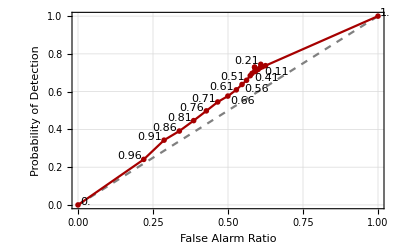
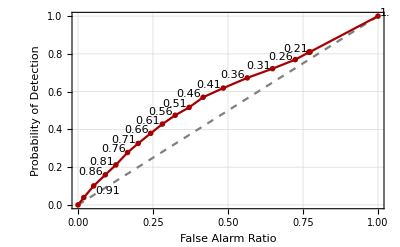
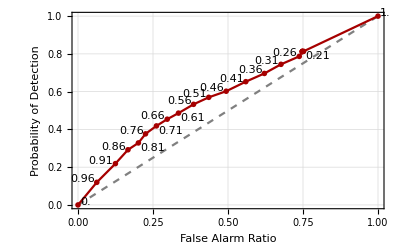
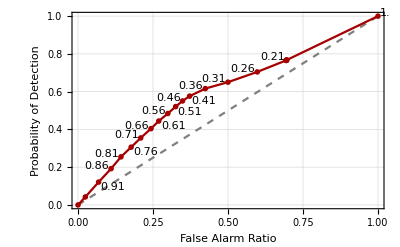
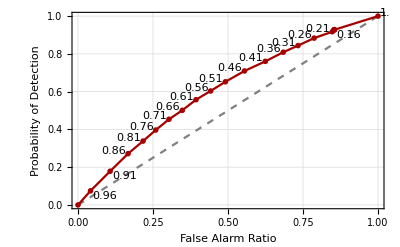
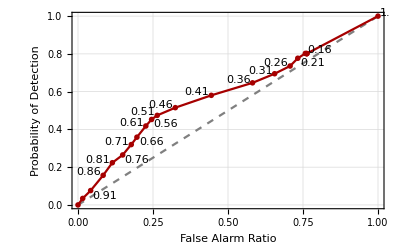
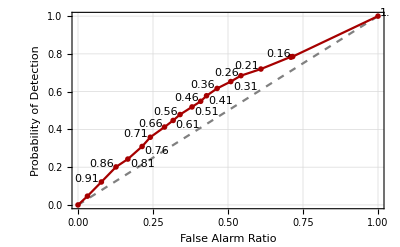
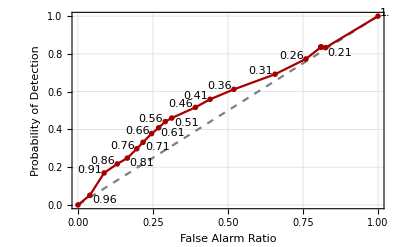
-Graphics-ROC Score=0.553BoM | -Graphics-ROC Score=0.583CMA | -Graphics-ROC Score=0.585ECCC
-Graphics-ROC Score=0.601ECMWF | -Graphics-ROC Score=0.607HCMR | -Graphics-ROC Score=0.587ISACCNR
-Graphics-ROC Score=0.584JMA | -Graphics-ROC Score=0.566KMA | -Graphics-ROC Score=0.586MeteoFrance
-Graphics-ROC Score=0.59NCEP | -Graphics-ROC Score=0.591UKMO | 0

```mathematica
Grid[ArrayReshape[
Map[Block[{test,day,grid},
	test=Import["/Users/lambda/Documents/Research/S2SEvaluation/Data/"<>#<>"/"<>#<>".mx"];
	day=30;
	grid=1;
	Labeled[ROC[Flatten[test[[1]][[;;,;;,day,grid]],1],
		Flatten[Table[test[[2]][[;;,day,grid]],Dimensions[test[[1]]][[1]]],1],0,"plot"],#,Top]]&,models],
{4,3}]]
```

## Implementation

Setting the Environment

```mathematica
SetDirectory["/Users/lambda/Documents/Research/S2SEvaluation/Data"];
models=Select[FileNames[],StringFreeQ[#,"."]&];
SCA=Map[Block[{grid=Import["/Users/lambda/Documents/Research/S2SEvaluation/Data/"<>#<>"/"<>#<>"_grids.mx"]},
	Map[#[[1]]&,Position[grid[[;;,1]],_?(#≤38.0&)]]]&,models];
NCA=Map[Block[{grid=Import["/Users/lambda/Documents/Research/S2SEvaluation/Data/"<>#<>"/"<>#<>"_grids.mx"]},
	Map[#[[1]]&,Position[grid[[;;,1]],_?(And[#>38.0,#<=42]&)]]]&,models];
OR=Map[Block[{grid=Import["/Users/lambda/Documents/Research/S2SEvaluation/Data/"<>#<>"/"<>#<>"_grids.mx"]},
	Map[#[[1]]&,Position[grid[[;;,1]],_?(And[#>42.0,#≤45]&)]]]&,models];
WA=Map[Block[{grid=Import["/Users/lambda/Documents/Research/S2SEvaluation/Data/"<>#<>"/"<>#<>"_grids.mx"]},
	Map[#[[1]]&,Position[grid[[;;,1]],_?(#>45&)]]]&,models];
```

Build the Main Function

```mathematica
Evaluation[dataset_,type_,season_:0,interval_:{1,1},grids_:{1},skill_:Correlation]:=Block[{grid,simu,obser,msimu},
	(*type: grid&daily,grid&interval,regional&daily,regional&interval*)
	grid=Import["/Users/lambda/Documents/Research/S2SEvaluation/Data/"<>dataset<>"/"<>dataset<>"_grids.mx"];
	{simu,obser}=Block[{osimu,oobser},
		{osimu, oobser} = Import["/Users/lambda/Documents/Research/S2SEvaluation/Data/"<>dataset<>"/"<>dataset<>".mx"];
		If[season==0,
		{osimu,oobser},
		Block[{winter,time},
			time=Import["/Users/lambda/Documents/Research/S2SEvaluation/Data/" <> dataset <> "/" <> dataset <> "_control_time.mx"];
		    winter=Map[#[[1]]&,Position[time[[;;,2]],_?(Or[#>=10,#≤3]&)]];
			{osimu[[;;,winter,;;,;;]],oobser[[winter,;;,;;]]}]]];
	msimu=Mean[simu];
	If[type=="grid&daily",
		Table[Table[skill[msimu[[;;,day,grid]],obser[[;;,day,grid]]],{day,Dimensions[obser][[-2]]}],{grid,Dimensions[obser][[-1]]}],
	If[type=="grid&interval",
		If[Dimensions[obser][[-2]]>=interval[[2]],
		Block[{isimu,imsimu,iobser},
			isimu=Mean[Transpose[Map[Transpose,simu]][[interval[[1]];;interval[[2]]]]];
			imsimu=Mean[isimu];
			iobser=Mean[Transpose[obser][[interval[[1]];;interval[[2]]]]];
			Table[skill[imsimu[[;;,grid]],iobser[[;;,grid]]],{grid,Dimensions[iobser][[-1]]}]],
		Table[0,{grid,Dimensions[obser][[-1]]}]],
	If[type=="regional&daily",
		Block[{rsimu,rmsimu,robser},
			rmsimu=Mean[Transpose[Map[Transpose,msimu]][[grids]]];
			robser=Mean[Transpose[Map[Transpose,obser]][[grids]]];
			Table[skill[rmsimu[[;;,g]],robser[[;;,g]]],{g,Dimensions[robser][[-1]]}]],
	If[type=="regional&interval",
		If[Dimensions[obser][[-2]]>=interval[[2]],
			Block[{rsimu,rmsimu,robser},
				rmsimu=Mean[Transpose[Mean[Transpose[Map[Transpose,msimu]][[grids]]]][[interval[[1]];;interval[[2]]]]];
				robser=Mean[Transpose[Mean[Transpose[Map[Transpose,obser]][[grids]]]][[interval[[1]];;interval[[2]]]]];
				skill[rmsimu,robser]],
			0],
		Null]]]]];
```

Mass Produce Numerical Result

```mathematica
MassCompute[skill_,season_:0]:=Block[{gd,gi,dd,di},
	gd=Block[{origin},
		origin=ParallelMap[Evaluation[#,"grid&daily",season,1,1,skill]&,models];
		Table[Table[Mean[origin[[i]][[region[[i]]]]],{i,Length[models]}],{region,{SCA,NCA,OR,WA}}]];
	
	gi=Block[{origin},
		origin=Table[ParallelMap[Evaluation[#,"grid&interval",season,i,1,skill]&,models],{i,{{2,2},{3,4},{5,8},{8,14},{15,28},{22,42},{29,56}}}];
	    ParallelMap[Transpose[Map[Mean[Transpose[#]]&,Table[origin[[;;,i,#[[i]]]],{i,Length[models]}]]]&,{SCA,NCA,OR,WA}]];
	
	dd=Map[ParallelTable[Evaluation[models[[i]],"regional&daily",season,{1,1},#[[i]],skill],{i,Length[models]}]&,
		{SCA,NCA,OR,WA}];
	
	di=ParallelMap[Table[Table[Evaluation[models[[j]],"regional&interval",season,i,#[[j]],skill],{j,Length[models]}],
	{i,{{2,2},{3,4},{5,8},{8,14},{15,28},{22,42},{29,56}}}]&,{SCA,NCA,OR,WA}];
	{gd,gi,dd,di}];
```

Mass Visualize

```mathematica
MassVisualize[skill_,range_]:=Block[{gd,gi,dd,di,gddraw,gidraw,dddraw,didraw,result,fig,label},
{gd,gi,dd,di}=MassCompute[ROC,0];

gddraw=ParallelMap[ListLinePlot[#,
	PlotStyle->Map[{#[[1]],Thickness[0.005]}&,datasets],
	PlotRange->range,
	BaseStyle->25,
	Frame->True,
	ImageSize->800,
	FrameLabel->{"Forecast Leading Day",ToString[skill]}]&,gd];

gidraw=ParallelMap[BarChart[#,
	BaseStyle->25,
	BarSpacing->{0,4.},
	ChartStyle->datasets[[;;,1]],
	ChartLabels->{{"1d1d","2d2d","4d4d","1w1w","2w2w","3w3w","4w4w"},None},
	Frame->True,
	PlotRange->range,
	FrameLabel->{"Forecast Interval",ToString[skill]},
	ImageSize->800]&,gi];

dddraw=ParallelMap[ListLinePlot[#,
	PlotStyle->Map[{#[[1]],Thickness[0.005]}&,datasets],
	BaseStyle->25,
	Frame->True,
	ImageSize->800,
	PlotRange->range,
	FrameLabel->{"Forecast Leading Day",ToString[skill]}]&,dd];

didraw=ParallelMap[BarChart[#,
	BaseStyle->25,
	BarSpacing->{0,4.},
	ChartStyle->datasets[[;;,1]],
	ChartLabels->{{"1d1d","2d2d","4d4d","1w1w","2w2w","3w3w","4w4w"},None},
	Frame->True,
	PlotRange->range,
	FrameLabel->{"Forecast Interval",ToString[skill]},
	ImageSize->800]&,di];

result=Map[Flatten,Table[{{gddraw[[i]],dddraw[[i]]},{gidraw[[i]],didraw[[i]]}},{i,4}]];
label=Block[{},
	table[pairs_] :=TableForm[Transpose[pairs],TableAlignments->Center];
	SwatchLegend[datasets[[;;,1]],datasets[[;;,2]],
	LegendLayout->table,
	LabelStyle->{FontSize->50},
	LegendMarkerSize->50]];
fig=Labeled[TableForm[result,
	TableHeadings->{Map[Style[#,FontSize->50]&,{"SCA","NCA","OR","WA"}],
		Map[Style[#,FontSize->50]&,{"Grid Daily Scale","Regional Daily Scale","Grid Interval Scale","Regional Interval Scale"}]},
	TableAlignments->Center],label,Bottom];
Export["/Users/lambda/Documents/Research/S2SEvaluation/Results/fig_<>"<>ToString[skill]<>".pdf",fig]];
```

## Results

### Corr

```mathematica
{gd,gi,dd,di}=MassCompute[Correlation,1];
```

Grid- Daily

```mathematica
gddraw=Map[ListLinePlot[#,
	PlotStyle->Map[{#[[1]],Thickness[0.005]}&,datasets],
	PlotRange->{0,0.9},
	BaseStyle->25,
	Frame->True,
	ImageSize->800,
	FrameLabel->{"Forecast Leading Day","Correlation with CPC Data"}]&,gd];
```

Grid- nDnD

```mathematica
gidraw=Map[BarChart[#,
	BaseStyle->25,
	BarSpacing->{0,4.},
	ChartStyle->datasets[[;;,1]],
	ChartLabels->{{"1d1d","2d2d","4d4d","1w1w","2w2w","3w3w","4w4w"},None},
	Frame->True,
	PlotRange->{0,0.9},
	FrameLabel->{"Forecast Interval","Correlation with CPC Data"},
	ImageSize->800]&,gi];
```

Climate Division- Daily

```mathematica
dddraw=Map[ListLinePlot[#,
	PlotStyle->Map[{#[[1]],Thickness[0.005]}&,datasets],
	BaseStyle->25,
	Frame->True,
	ImageSize->800,
	PlotRange->{0,0.9},
	FrameLabel->{"Forecast Leading Day","Correlation with CPC Data"}]&,dd];
```

Climate Division- Regional

```mathematica
didraw=Map[BarChart[#,
	BaseStyle->25,
	BarSpacing->{0,4.},
	ChartStyle->datasets[[;;,1]],
	ChartLabels->{{"1d1d","2d2d","4d4d","1w1w","2w2w","3w3w","4w4w"},None},
	Frame->True,
	PlotRange->{0,0.9},
	FrameLabel->{"Forecast Interval","Correlation with CPC Data"},
	ImageSize->800]&,di];
```

Export

```mathematica
result=Map[Flatten,Table[{{gddraw[[i]],dddraw[[i]]},{gidraw[[i]],didraw[[i]]}},{i,4}]];
label=Block[{},
	table[pairs_] := 
TableForm[Transpose[pairs],TableAlignments->Center];
	SwatchLegend[datasets[[;;,1]],datasets[[;;,2]],
	LegendLayout->table,
	LabelStyle->{FontSize->50},
	LegendMarkerSize->50]];
fig2=Labeled[TableForm[result,
	TableHeadings->{Map[Style[#,FontSize->50]&,{"SCA","NCA","OR","WA"}],
		Map[Style[#,FontSize->50]&,{"Grid Daily Scale","Regional Daily Scale","Grid Interval Scale","Regional Interval Scale"}]},
	TableAlignments->Center],label,Bottom];
```

```mathematica
Export["/Users/lambda/Documents/Research/S2SEvaluation/Results/fig2_corr.pdf",fig2]
```

/Users/lambda/Documents/Research/S2SEvaluation/Results/fig2_corr.pdf

## RMSE

```mathematica
RMSE[simu_,obser_,linearcorrection_:1]:=
	If[linearcorrection≠0,
		RMSE[Block[{model,xx},
			model=LinearModelFit[Transpose[{simu,obser}],xx,xx];
			model/@simu],obser,0],
	Sqrt[Mean[(simu-obser)^2]]]
```

```mathematica
{gd,gi,dd,di}=MassCompute[RMSE,1];
```

Grid- Daily

```mathematica
gddraw=Table[ListLinePlot[gd[[i]],
	PlotStyle->Map[{#[[1]],Thickness[0.005]}&,datasets],
	PlotRange->range[[i]],
	BaseStyle->25,
	Frame->True,
	ImageSize->800,
	FrameLabel->{"Forecast Leading Day",name}],{i,4}];
```

Grid- nDnD

```mathematica
gidraw=Table[BarChart[gi[[i]],
	BaseStyle->25,
	BarSpacing->{0,4.},
	ChartStyle->datasets[[;;,1]],
	ChartLabels->{{"1d1d","2d2d","4d4d","1w1w","2w2w","3w3w","4w4w"},None},
	Frame->True,
	PlotRange->range[[i]],
	FrameLabel->{"Forecast Interval",name},
	ImageSize->800],{i,4}];
```

Climate Division- Daily

```mathematica
dddraw=Table[ListLinePlot[dd[[i]],
	PlotStyle->Map[{#[[1]],Thickness[0.005]}&,datasets],
	BaseStyle->25,
	Frame->True,
	ImageSize->800,
	PlotRange->range[[i]],
	FrameLabel->{"Forecast Leading Day",name}],{i,4}];
```

Climate Division- Regional

```mathematica
didraw=Table[BarChart[di[[i]],
	BaseStyle->25,
	BarSpacing->{0,4.},
	ChartStyle->datasets[[;;,1]],
	ChartLabels->{{"1d1d","2d2d","4d4d","1w1w","2w2w","3w3w","4w4w"},None},
	Frame->True,
	PlotRange->range[[i]],
	FrameLabel->{"Forecast Interval",name},
	ImageSize->800],{i,4}];
```

Export

```mathematica
result=Map[Flatten,Table[{{gddraw[[i]],dddraw[[i]]},{gidraw[[i]],didraw[[i]]}},{i,4}]];
label=Block[{},
	table[pairs_] := 
TableForm[Transpose[pairs],TableAlignments->Center];
	SwatchLegend[datasets[[;;,1]],datasets[[;;,2]],
	LegendLayout->table,
	LabelStyle->{FontSize->50},
	LegendMarkerSize->50]];
fig4=Labeled[TableForm[result,
	TableHeadings->{Map[Style[#,FontSize->50]&,{"SCA","NCA","OR","WA"}],
		Map[Style[#,FontSize->50]&,{"Grid Daily Scale","Regional Daily Scale","Grid Interval Scale","Regional Interval Scale"}]},
	TableAlignments->Center],label,Bottom];
```

```mathematica
Export["/Users/lambda/Documents/Research/S2SEvaluation/Results/fig4_LinearRMSE.pdf",fig4]
```

/Users/lambda/Documents/Research/S2SEvaluation/Results/fig4_LinearRMSE.pdf

## NSE

```mathematica
NSE[simu_,obser_,linearcorrection_:1]:=
	If[linearcorrection≠0,
		NSE[Block[{model,xx},
			model=LinearModelFit[Transpose[{simu,obser}],xx,xx];
			model/@simu],obser,0],
	Block[{m=Mean[obser]},1.-Total[(simu-obser)^2]/Total[(obser-m)^2]]];
```

```mathematica
{gd,gi,dd,di}=MassCompute[NSE];
```

```mathematica
range=Table[MinMax[{gd[[i]],gi[[i]],dd[[i]],di[[i]]}],{i,4}]
name="NSE"
```

NSE

```mathematica
range=Table[{0,0.8},4]
```

{{0,0.8},{0,0.8},{0,0.8},{0,0.8}}

Grid- Daily

{{0,0.78868},{0,0.764987},{0,0.722273},{0,0.811715}}

```mathematica
gddraw=Table[ListLinePlot[gd[[i]],
	PlotStyle->Map[{#[[1]],Thickness[0.005]}&,datasets],
	PlotRange->range[[i]],
	BaseStyle->25,
	Frame->True,
	ImageSize->800,
	FrameLabel->{"Forecast Leading Day",name}],{i,4}];
```

Grid- nDnD

```mathematica
gidraw=Table[BarChart[gi[[i]],
	BaseStyle->25,
	BarSpacing->{0,4.},
	ChartStyle->datasets[[;;,1]],
	ChartLabels->{{"1d1d","2d2d","4d4d","1w1w","2w2w","3w3w","4w4w"},None},
	Frame->True,
	PlotRange->range[[i]],
	FrameLabel->{"Forecast Interval",name},
	ImageSize->800],{i,4}];
```

Climate Division- Daily

```mathematica
dddraw=Table[ListLinePlot[dd[[i]],
	PlotStyle->Map[{#[[1]],Thickness[0.005]}&,datasets],
	BaseStyle->25,
	Frame->True,
	ImageSize->800,
	PlotRange->range[[i]],
	FrameLabel->{"Forecast Leading Day",name}],{i,4}];
```

Climate Division- Regional

```mathematica
didraw=Table[BarChart[di[[i]],
	BaseStyle->25,
	BarSpacing->{0,4.},
	ChartStyle->datasets[[;;,1]],
	ChartLabels->{{"1d1d","2d2d","4d4d","1w1w","2w2w","3w3w","4w4w"},None},
	Frame->True,
	PlotRange->range[[i]],
	FrameLabel->{"Forecast Interval",name},
	ImageSize->800],{i,4}];
```

Export

```mathematica
result=Map[Flatten,Table[{{gddraw[[i]],dddraw[[i]]},{gidraw[[i]],didraw[[i]]}},{i,4}]];
label=Block[{},
	table[pairs_] := 
TableForm[Transpose[pairs],TableAlignments->Center];
	SwatchLegend[datasets[[;;,1]],datasets[[;;,2]],
	LegendLayout->table,
	LabelStyle->{FontSize->50},
	LegendMarkerSize->50]];
fig6=Labeled[TableForm[result,
	TableHeadings->{Map[Style[#,FontSize->50]&,{"SCA","NCA","OR","WA"}],
		Map[Style[#,FontSize->50]&,{"Grid Daily Scale","Regional Daily Scale","Grid Interval Scale","Regional Interval Scale"}]},
	TableAlignments->Center],label,Bottom];
```

```mathematica
Export["/Users/lambda/Documents/Research/S2SEvaluation/Results/fig6_LinearNSE2.pdf",fig6]
```

/Users/lambda/Documents/Research/S2SEvaluation/Results/fig6_LinearNSE.pdf

## Seeking Forecast windows

## Conclusion

For a fair comparison across a seamless range of time scales, the verification is performed using data averaged over time windows equal in length to the forecast lead time. At a lead time of one day, skill is greatest in the extratropics around 40-60o latitude, lowest around 20o, and has a secondary local maximum close to the equator. The extratropical skill at this short range is highest in the winter hemisphere presumably due to the higher predictability of winter baroclinic systems.

defining a consistent and useful distance metric on these aspects

The essence of our approach is as follows. We compute the prediction skill at
 a range of lead times, from one day to one month. As the lead time increases, we also
 increase the length of the time window over which the data are averaged for
 verification. This is intended to capture the fact that we are transitioning from
 weather to climate prediction as the lead time increases, and to allow the transition to
 occur smoothly. The skill is computed for both total precipitation and anomalies, and
 comparison is made with the skill achievable by a persistence forecast of the
 precipitation anomalies. For comparison we also evaluate the forecasts at varying lead
time but with a fixed verification window of 1 day.

Deterministic

```mathematica
dataset="ECMWF";
	season=1;
	grid=Import["/Users/lambda/Documents/Research/S2SEvaluation/Data/"<>dataset<>"/"<>dataset<>"_grids.mx"];
	{simu,obser}=Block[{osimu,oobser},
		{osimu, oobser} = Import["/Users/lambda/Documents/Research/S2SEvaluation/Data/"<>dataset<>"/"<>dataset<>".mx"];
		If[season==0,
		{osimu,oobser},
		Block[{winter,time},
			time=Import["/Users/lambda/Documents/Research/S2SEvaluation/Data/" <> dataset <> "/" <> dataset <> "_control_time.mx"];
		    winter=Map[#[[1]]&,Position[time[[;;,2]],_?(Or[#>=10,#≤3]&)]];
			{osimu[[;;,winter,;;,;;]],oobser[[winter,;;,;;]]}]]];
	msimu=Mean[simu];
```

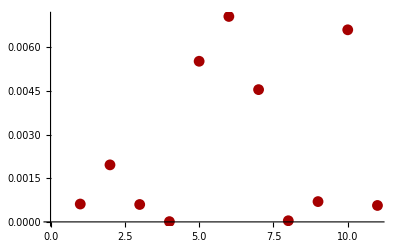

```mathematica
day=46;
grid=3;
ListPlot[Table[NSE[simu[[ensemble,;;,day,grid]],obser[[;;,day,grid]]],{ensemble,11}]]
```